# Mathématica 5

```mathematica
Quit[]
```

```mathematica
f[x_]:=If[x>0,Exp[-x^2],1]
```

```mathematica
f[10]
```

1/ⅇ^100

```mathematica
f[-1]
```

1

```mathematica
Clear[f]
```

```mathematica
"f[x_/;condition]:=expression[x]"
"Which"
```

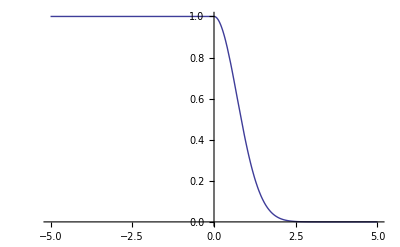

```mathematica
Clear[f]
f[x_/;x>0]:=Exp[-x^2];
f[x_/;x≤0]:=1;
Plot[f[x],{x,-5,5}]
```

```mathematica
Clear[f]
```

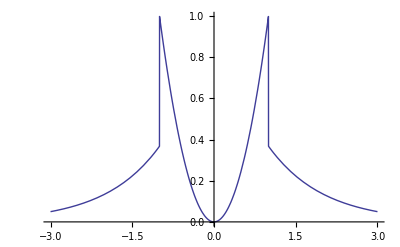

```mathematica
g[x_/;Abs[x]>1]:=Exp[-Abs[x]];
g[x_/;x=1]:=0;
g[x_/;x=-1]:=0;
g[x_/;-1<x<1]:=x^2;
Plot[g[x],{x,-3,3}]
```

```mathematica
Clear[g]
```

```mathematica
fact[0]=1;
fact[n_]:=n*fact[n-1]
```

```mathematica
f1[0]=0;
f1[n_]:=f1[n-1]+n
```

```mathematica
f1[10]
```

55

```mathematica
Clear[f1]
```

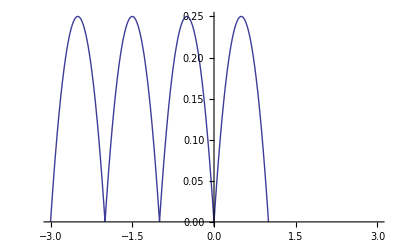

```mathematica
Clear[f]
f[x_/;(0≤x)&&(x<1)]:=x*(1-x);
f[x_/;x<0]:=f[x+1];
Plot[f[x],{x,-3,3}]
```

```mathematica
vecteur1={1,2,3,4}
```

{1,2,3,4}

```mathematica
vecteur2={e1,e2,e3,e4}
```

{e1,e2,e3,e4}

```mathematica
maMatrice={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[maMatrice]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
maMatrice[[2]]
```

{4,5,6}

```mathematica
maMatrice[[2,1]]
```

4

```mathematica
maMatrice[[3,2]]
```

8

```mathematica
"Dimensions[A]
Length[A]
MatrixForm
IdentityMatrix
DiagonaMatrix"
```

```mathematica
IdentityMatrix[10]
```

{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}}

```mathematica
MatrixForm[IdentityMatrix[15]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
DiagonalMatrix[{a,b,c,d},2]//MatrixForm
```

(0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | b | 0 | 0
0 | 0 | 0 | 0 | c | 0
0 | 0 | 0 | 0 | 0 | d
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[i,{i,1,3},{j,1,4}]//MatrixForm
```

(1 | 1 | 1 | 1
2 | 2 | 2 | 2
3 | 3 | 3 | 3)

```mathematica
Table[Random[],{i,1,3},{j,1,4}]//MatrixForm
```

(0.0697939 | 0.0492474 | 0.427545 | 0.943702
0.32602 | 0.277071 | 0.97584 | 0.826418
0.772656 | 0.118156 | 0.529976 | 0.729235)

```mathematica
fonctionMatrice[n_]:=Table[1,{i,1,n},{j,1,n}]//MatrixForm
```

```mathematica
fonctionMatrice[12]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
fonctionMatrice2[n_]:=Table[1/(i+j-1),{i,1,n},{j,1,n}]//MatrixForm
```

```mathematica
fonctionMatrice2[12]
```

(1 | 1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12
1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13
1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14
1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15
1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16
1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17
1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18
1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19
1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19 | 1/20
1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19 | 1/20 | 1/21
1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19 | 1/20 | 1/21 | 1/22
1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19 | 1/20 | 1/21 | 1/22 | 1/23)

```mathematica
fonctionMatrice3[n_]:=Table[If[i≤j,1,0],{i,1,n},{j,1,n}]//MatrixForm
```

```mathematica
fonctionMatrice3[10]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
fonctionMatrice4[n_]:=Table[If[i≤j,j-i+1,0],{i,1,n},{j,1,n}]//MatrixForm
```

```mathematica
fonctionMatrice4[10]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
0 | 0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0 | 1 | 2 | 3 | 4 | 5 | 6
0 | 0 | 0 | 0 | 0 | 1 | 2 | 3 | 4 | 5
0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 3 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
fonctionMatrice5[n_]:=Table[If[i==j,0,1],{i,1,n},{j,1,n}]//MatrixForm
```

```mathematica
fonctionMatrice5[20]
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)

```mathematica
Clear[fonctionMatrice]
Clear[fonctionMatrice2]
Clear[fonctionMatrice3]
Clear[fonctionMatrice4]
Clear[fonctionMatrice5]
```

```mathematica
vecteur1+vecteur2
```

{1+e1,2+e2,3+e3,4+e4}

```mathematica
c*vecteur2
```

{c e1,c e2,c e3,c e4}

```mathematica
l=Table[2*k*Pi/6,{k,1,6}]
```

{π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,2 π}

```mathematica
Sin[l]
```

{(√3)/2,(√3)/2,0,-(√3)/2,-(√3)/2,0}

```mathematica
A=Table[1,{3},{3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
A*A
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
A.A
```

{{3,3,3},{3,3,3},{3,3,3}}

```mathematica
Dot[A,A]
```

{{3,3,3},{3,3,3},{3,3,3}}

```mathematica
MatrixPower[A,10]
```

{{19683,19683,19683},{19683,19683,19683},{19683,19683,19683}}

```mathematica
"Inverse[A] équivaut à MatrixPower[A,-1]"
```

```mathematica
Clear[A]
```

```mathematica
R:={{5,2},{-4,-1}}
```

```mathematica
R//MatrixForm
```

(5 | 2
-4 | -1)

```mathematica
Det[R]
```

3

```mathematica
"Det[R]!=0 donc R est inversible.
R est une matrice carrée donc R^-1=(-1/Det[R])*{{-1,-2},{4,5}}"
```

```mathematica
Inverse[R]//MatrixForm
```

(-1/3 | -2/3
4/3 | 5/3)

```mathematica
Clear[A]
A={{1,-2,3,2},{0,1,-1,-1},{1,0,1,0}}
```

{{1,-2,3,2},{0,1,-1,-1},{1,0,1,0}}

```mathematica
A//MatrixForm
```

(1 | -2 | 3 | 2
0 | 1 | -1 | -1
1 | 0 | 1 | 0)

```mathematica
NullSpace[A]
```

{{0,1,0,1},{-1,1,1,0}}

## Exercices divers au choix

```mathematica
x[0]=1;
x[1]=1;
x[2]=1;
x[3]=0;
x[n_]:=x[n-1]-2*x[n-3]
```

```mathematica
Table[x[n],{n,1,10}]
```

{1,1,0,-2,-4,-4,0,8,16,16}

```mathematica
Clear[x]
```

```mathematica
H[1]={x[0]};
H[n_]:=Table[x[i-1+j],{i,1,n},{j,1,n}]
```

```mathematica
H[10]//MatrixForm
```

(1 | 1 | 0 | -2 | -4 | -4 | 0 | 8 | 16 | 16
1 | 0 | -2 | -4 | -4 | 0 | 8 | 16 | 16 | 0
0 | -2 | -4 | -4 | 0 | 8 | 16 | 16 | 0 | -32
-2 | -4 | -4 | 0 | 8 | 16 | 16 | 0 | -32 | -64
-4 | -4 | 0 | 8 | 16 | 16 | 0 | -32 | -64 | -64
-4 | 0 | 8 | 16 | 16 | 0 | -32 | -64 | -64 | 0
0 | 8 | 16 | 16 | 0 | -32 | -64 | -64 | 0 | 128
8 | 16 | 16 | 0 | -32 | -64 | -64 | 0 | 128 | 256
16 | 16 | 0 | -32 | -64 | -64 | 0 | 128 | 256 | 256
16 | 0 | -32 | -64 | -64 | 0 | 128 | 256 | 256 | 0)

```mathematica
MatrixRank[H[2]]
```

2

```mathematica
MatrixRank[H[3]]
```

2

```mathematica
Table[MatrixRank[H[n]],{n,2,10}]
```

{2,2,2,2,2,2,2,2,2}

```mathematica
Clear[H]
```

```mathematica
x2[0]=1/2;
x2[1]=1;
x2[2]=1;
x2[3]=0;
x2[n_]:=x2[n-1]-2*x2[n-3]
```

```mathematica
H2[1]={x2[0]};
H2[n_]:=Table[x2[i-1+j],{i,1,n},{j,1,n}]
```

```mathematica
H2[5]//MatrixForm
```

(1 | 1 | 0 | -2 | -4
1 | 0 | -2 | -4 | -4
0 | -2 | -4 | -4 | 0
-2 | -4 | -4 | 0 | 8
-4 | -4 | 0 | 8 | 16)

```mathematica
Table[MatrixRank[H2[n]],{n,2,10}]
```

{2,2,2,2,2,2,2,2,2}

```mathematica
Clear[x2]
Clear[H2]
```

## Q6

```mathematica
A1={{-1,0,1},{1,-1,0},{0,1,-1}}
```

{{-1,0,1},{1,-1,0},{0,1,-1}}

```mathematica
A1//MatrixForm
```

(-1 | 0 | 1
1 | -1 | 0
0 | 1 | -1)

```mathematica
B=Transpose[A1]
```

{{-1,1,0},{0,-1,1},{1,0,-1}}

```mathematica
B//MatrixForm
```

(-1 | 1 | 0
0 | -1 | 1
1 | 0 | -1)

```mathematica
A1.B//MatrixForm
```

(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2)

```mathematica
B.A1//MatrixForm
```

(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2)

```mathematica
A1.A1//MatrixForm
```

(1 | 1 | -2
-2 | 1 | 1
1 | -2 | 1)

```mathematica
B.B//MatrixForm
```

(1 | -2 | 1
1 | 1 | -2
-2 | 1 | 1)